Classical and Quantum Description of Plasma and Radiation in Strong Fields , PhD Thesis

Fabien Niel et al 2021 Springer Theses https://link.springer.com/book/10.1007/978-3-030-73547-0
Notebook: Óscar Amaro, September 2023 @ GoLP-EPP

Introduction
Some calculations.

## Figure 8.1

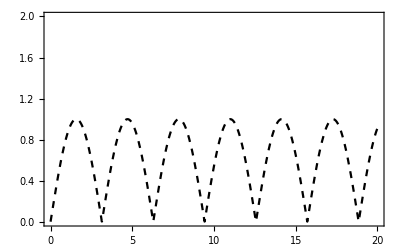

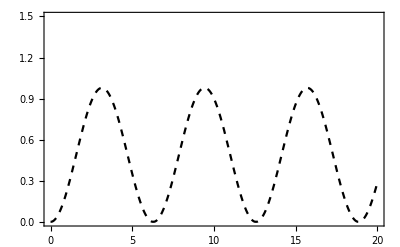

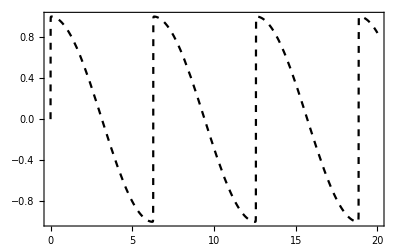

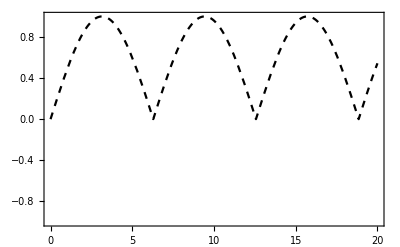

```mathematica
Clear[a0,γ,χ,βy,βz,t]
a0=500;

(*Attention: mistake in the Thesis in γ expression ? *)
γ=Sqrt[1+a0^2 Sin[t]^2];
Plot[γ/a0,{t,0,20},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False,PlotRange->{0,+2}]

(* ω0=1eV?? *)
χ=1/(0.511 10^6)  a0 Sqrt[1+4a0^2 Sin[t/2]^4];
Plot[χ,{t,0,20},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False,PlotRange->{0,+1.5}]

βy=(a0 Sin[t])/Sqrt[1+4a0^2 Sin[t/2]^2];
Plot[βy,{t,0,20},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False,PlotRange->{-1,+1}]

βz=(a0 (1-Cos[t]))/Sqrt[1+4a0^2 Sin[t/2]^2];
Plot[βz,{t,0,20},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False,PlotRange->{-1,+1}]
```

## Figure 8.3 Asymptotic expressions

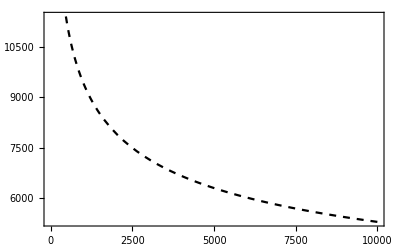

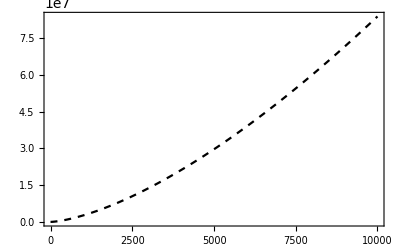

-Graphics-

```mathematica
Clear[a0,γ,χ,βy,βz,t,A,α]
aS=400000;
α=1/137;
A=2/3 α;
γas = Sqrt[aS]( a0/(0.56 A))^0.75 ;
βEas = Sqrt[a0-Sqrt[a0]aS/(0.56 A)^1.5];
χas = a0^1.5/(0.56 A)^0.75;

Plot[γas/a0,{a0,0,10000},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False](*PlotRange->{0,+1}*)

Plot[χas,{a0,0,10000},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False](*PlotRange->{0,+30}*)

Plot[βEas,{a0,0,10000},PlotStyle->Directive[Black,Dashed],Frame->True,Axes->False](*PlotRange->{0,+1}*)
```

## Figure 8.4

We try to reproduce figure 8.4 from Fabien Niel’s PhD thesis. The text in the textbook might have some omissions and changes in notation. We are able to reproduce the S type curve, but the asymptotic value is not the one in the text.

Also, it’s possible to derive the σe∞ for χ<<1 using the χ<<1 expressions for S and h σ~0.8 √(χ/(2-3 χ))

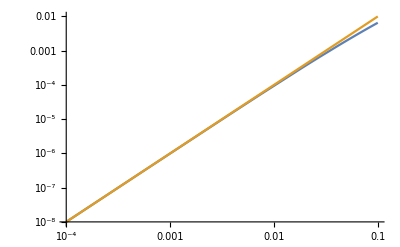

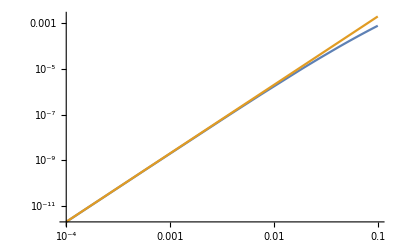

```mathematica
Clear[α,τ,χ,g,h,S,dh,dS,dχ]
Clear[m,c,re]

g[χ_?NumericQ]:=g[χ]=(9√3)/(8π)NIntegrate[(2ν^2 BesselK[5/3,ν])/(2+3ν χ)^2+(4ν(3ν χ)^2)/(2+3ν χ)^4 BesselK[2/3,ν],{ν,0,∞}]
S[χ_?NumericQ]:=S[χ]=χ^2 g[χ]
h[χ_?NumericQ]:=h[χ]=(9√3)/(4π)NIntegrate[(2χ^3 ν^3 BesselK[5/3,ν])/(2+3ν χ)^3+(54 χ^5 ν^4)/(2+3ν χ)^5 BesselK[2/3,ν],{ν,0,∞}]

LogLogPlot[{S[χ],χ^2},{χ,10^-4,10^-1},PlotPoints->2]

LogLogPlot[{h[χ],2χ^3},{χ,10^-4,10^-1},PlotPoints->2]
```

```mathematica
Clear[α,τ,χ,g,h,S,dh,dS,dχ,tab,tabapp,σapp,σeinf]
Clear[m,c,re]

g[χ_]:=(9√3)/(8π)NIntegrate[(2ν^2 BesselK[5/3,ν])/(2+3ν χ)^2+(4ν(3ν χ)^2)/(2+3ν χ)^4 BesselK[2/3,ν],{ν,0,∞}]
S[χ_]:=χ^2 g[χ]
h[χ_]:=(9√3)/(4π)NIntegrate[(2χ^3 ν^3 BesselK[5/3,ν])/(2+3ν χ)^3+(54 χ^5 ν^4)/(2+3ν χ)^5 BesselK[2/3,ν],{ν,0,∞}]

dχ=0.0000001;
dh[x_]:=(h[x+dχ]-h[x-dχ])/(2 dχ)
dS[x_]:=(S[x+dχ]-S[x-dχ])/(2 dχ)

(*equation (8.25) of Fabien Niel's thesis *)
σeinf[χavg_]:=Sqrt[h[χavg]/(1.55χavg (2dS[χavg]-dh[χavg]))]//Quiet
σapp[χ_]:=0.8032193289024989 √(χ/(2-3 χ))(*Sqrt[(2χ^3)/(1.55 χ(2 2χ-6χ^2))]*)
```

```mathematica
tab=ParallelTable[{10^χ,σeinf[10^χ]},{χ,-6,4.5,0.5}];
tabapp=ParallelTable[{10^χ,σapp[10^χ]},{χ,-6,4.5,0.5}];
```

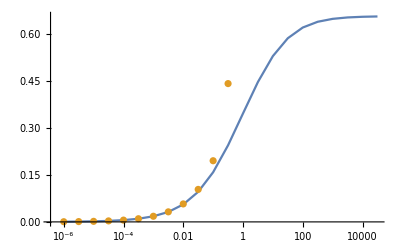

```mathematica
ListLogLinearPlot[{tab,tabapp},Joined->{True,False}]
```